## Notebook for calculation of isosteric enthalpy of adsorption from variable temperature isotherms

Written using Mathematica 11

As published in https://pubs.acs.org/doi/10.1021/jacs.1c07449

Divergent Adsorption Behavior Controlled by Primary Coordination Sphere Anions in the Metal–Organic Framework Ni2X2BTDD
Julius J. Oppenheim, Jenna L. Mancuso, Ashley M. Wright, Adam J. Rieth, Christopher H. Hendon, and Mircea Dincǎ

#### Import data from Excel file

```mathematica
s=Import[".../NiClBTDD_CO_VT_data.xlsx"];
```

#### Parse the Excel file, loading each pressure and quantity adsorbed into an array. In this example, the data has already been converted into kPa and mmol/g in the Excel file.

Parsing an Excel file proceeds at the following
s[[a]][[All,b]][[c;;d]] with ‘a’ is the Excel page, ‘b’ is the column number, ‘c’ is the first row, and ‘d’ is the last row. Counting starts at 1.

```mathematica
p283=s[[2]][[All,1]][[4;;44]] ; (* Pressure at 283K in units of kPa *)
q283=s[[2]][[All,3]][[4;;44]]; (* Quantity adsorbed at 283 K in units of mmol/g *)
p288=s[[2]][[All,5]][[4;;44]];
q288=s[[2]][[All,7]][[4;;44]];
p293=s[[2]][[All,9]][[4;;44]];
q293=s[[2]][[All,11]][[4;;44]];
p298=s[[2]][[All,13]][[4;;43]];
q298=s[[2]][[All,15]][[4;;43]];
p308=s[[2]][[All,17]][[4;;43]];
q308=s[[2]][[All,19]][[4;;43]];
```

#### Make an array of ‘quantity adsorbed’ points to which the isosteric enthalpy will be calculated in the final result (mmol/g).

Remember to not extrapolate outside of the experimentally measured quantities. In this example, the minimum experimentally measured quantity adsorbed is around 0.001 and maximum is 3.

```mathematica
plist={0.01,0.05,0.1,0.15,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.0,2.1,2.2,2.3,2.4,2.5};
```

#### Fit the data to a model. In this case, the Unilan function. The data is weighted as 1/‘quantity adsorbed’ as the fit at small pressures will dictate the accuracy of the zero-pressure isosteric enthalpy of adsorption.

```mathematica
udnlm283=NonlinearModelFit[Transpose@{p283,q283},{u/(2*ss)*Log[(1+1/a*p*Exp[ss])/(1+1/a*p*Exp[-ss])]},{{u,5},{ss,2},{a,10}},p,MaxIterations->50000,Weights->1/q283];
udnlm288=NonlinearModelFit[Transpose@{p288,q288},{u/(2*ss)*Log[(1+1/a*p*Exp[ss])/(1+1/a*p*Exp[-ss])]},{{u,5},{ss,2},{a,10}},p,MaxIterations->50000,Weights->1/q288];
udnlm293=NonlinearModelFit[Transpose@{p293,q293},{u/(2*ss)*Log[(1+1/a*p*Exp[ss])/(1+1/a*p*Exp[-ss])]},{{u,5},{ss,2},{a,10}},p,MaxIterations->50000,Weights->1/q293];
udnlm298=NonlinearModelFit[Transpose@{p298,q298},{u/(2*ss)*Log[(1+1/a*p*Exp[ss])/(1+1/a*p*Exp[-ss])]},{{u,5},{ss,2},{a,10}},p,MaxIterations->50000,Weights->1/q298];
udnlm308=NonlinearModelFit[Transpose@{p308,q308},{u/(2*ss)*Log[(1+1/a*p*Exp[ss])/(1+1/a*p*Exp[-ss])]},{{u,25},{ss,2},{a,100}},p,MaxIterations->50000,Weights->1/q308];
```

#### Inspect the results from the fit. The R2 value should be above 0.999

```mathematica
udnlm283["BestFitParameters"]
udnlm288["BestFitParameters"]
udnlm293["BestFitParameters"]
udnlm298["BestFitParameters"]
udnlm308["BestFitParameters"]
udnlm283["RSquared"]
udnlm288["RSquared"]
udnlm293["RSquared"]
udnlm298["RSquared"]
udnlm308["RSquared"]
udnlm283["ParameterTable"]
udnlm288["ParameterTable"]
udnlm293["ParameterTable"]
udnlm298["ParameterTable"]
udnlm308["ParameterTable"]
```

{u→5.0222,ss→2.58975,a→44.5242}

{u→5.19379,ss→2.62905,a→62.6492}

{u→5.72677,ss→2.88274,a→105.847}

{u→7.27046,ss→3.67202,a→307.017}

{u→24.9203,ss→12.1511,a→2.48772×10^6}

0.999995

0.999995

0.999996

0.999967

0.999986

| Estimate | Standard Error | t-Statistic | P-Value
u | 5.0222 | 0.0422817 | 118.78 | 1.83331×10^-50
ss | 2.58975 | 0.0301689 | 85.8417 | 4.01023×10^-45
a | 44.5242 | 1.16209 | 38.3139 | 5.64831×10^-32

| Estimate | Standard Error | t-Statistic | P-Value
u | 5.19379 | 0.0656771 | 79.0808 | 8.90536×10^-44
ss | 2.62905 | 0.0431202 | 60.9703 | 1.61718×10^-39
a | 62.6492 | 2.41858 | 25.9032 | 9.42768×10^-26

| Estimate | Standard Error | t-Statistic | P-Value
u | 5.72677 | 0.142864 | 40.0853 | 1.05581×10^-32
ss | 2.88274 | 0.0834327 | 34.5517 | 2.57712×10^-30
a | 105.847 | 8.34244 | 12.6878 | 3.0986×10^-15

| Estimate | Standard Error | t-Statistic | P-Value
u | 7.27046 | 2.72244 | 2.67057 | 0.0111855
ss | 3.67202 | 1.42177 | 2.58271 | 0.0138932
a | 307.017 | 432.18 | 0.710391 | 0.481916

| Estimate | Standard Error | t-Statistic | P-Value
u | 24.9203 | 0.0517708 | 481.357 | 7.48311×10^-72
ss | 12.1511 | 0.00449346 | 2704.18 | 1.38451×10^-99
a | 2.48772×10^6 | 4.09548×10^-8 | 6.07429×10^13 | 1.37184274461721×10^-482

#### Mean Absolute Percentage Error (MAPE, %) for all fits. Should be < 5%

```mathematica
mape283=0;
For[i=1,i<Length[p283]+1,i++,mape283+=Abs[(q283[[i]]-udnlm283[p283[[i]]])/q283[[i]]]]
mape283=mape283/Length[p283]*100;
mape288=0;
For[i=1,i<Length[p288]+1,i++,mape288+=Abs[(q288[[i]]-udnlm288[p288[[i]]])/q288[[i]]]]
mape288=mape288/Length[p288]*100;
mape293=0;
For[i=1,i<Length[p293]+1,i++,mape293+=Abs[(q293[[i]]-udnlm293[p293[[i]]])/q293[[i]]]]
mape293=mape293/Length[p293]*100;
mape298=0;
For[i=1,i<Length[p298]+1,i++,mape298+=Abs[(q298[[i]]-udnlm298[p298[[i]]])/q298[[i]]]]
mape298=mape298/Length[p298]*100;
mape308=0;
For[i=1,i<Length[p308]+1,i++,mape308+=Abs[(q308[[i]]-udnlm308[p308[[i]]])/q308[[i]]]]
mape308=mape308/Length[p308]*100;
(mape283+mape288+mape293+mape298+mape308)/5
```

1.61171

#### Linear-linear plot of data with fits

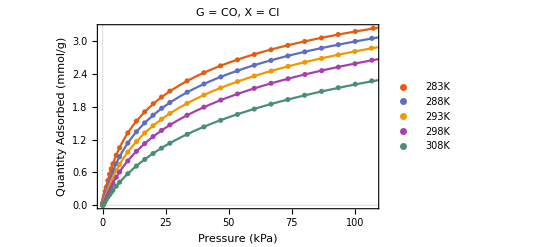

```mathematica
Show[ListPlot[{Transpose@{p283,q283},Transpose@{p288,q288},Transpose@{p293,q293},Transpose@{p298,q298},Transpose@{p308,q308}},PlotTheme->"Scientific",FrameLabel->{"Pressure (kPa)","Quantity Adsorbed (mmol/g)"},PlotLabel->"G = CO, X = Cl",PlotLegends->Placed[{"283K","288K","293K","298K","308K"},{Left,Center}]],Plot[{udnlm283[x],udnlm288[x],udnlm293[x],udnlm298[x],udnlm308[x]},{x,0.00001,150},PlotTheme->"Scientific"],ImageSize->Full,FrameStyle->Black]
```

#### Log-log plot of data and fits. The log-log plot is necessary to visualize the fit at low pressures.

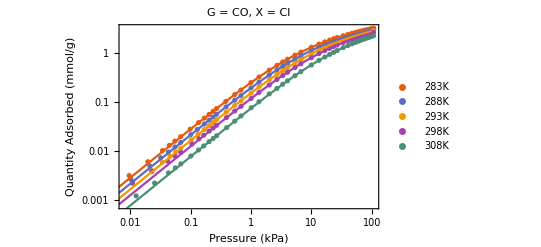

```mathematica
Show[ListLogLogPlot[{Transpose@{p283,q283},Transpose@{p288,q288},Transpose@{p293,q293},Transpose@{p298,q298},Transpose@{p308,q308}},PlotTheme->"Scientific",FrameLabel->{"Pressure (kPa)","Quantity Adsorbed (mmol/g)"},PlotLabel->"G = CO, X = Cl",PlotLegends->Placed[{"283K","288K","293K","298K","308K"},{Left,Center}]],LogLogPlot[{udnlm283[x],udnlm288[x],udnlm293[x],udnlm298[x],udnlm308[x]},{x,0.00001,100},PlotTheme->"Scientific"],ImageSize->Full,FrameStyle->Black]
```

#### Plot the residuals from the fit.

```mathematica
ListPlot[{Transpose@{p283,udnlm283["FitResiduals"]},Transpose@{p288,udnlm288["FitResiduals"]},Transpose@{p293,udnlm293["FitResiduals"]},Transpose@{p298,udnlm298["FitResiduals"]},Transpose@{p308,udnlm308["FitResiduals"]}},PlotTheme->"Scientific",FrameLabel->{"Pressure (kPa)","Residual Quantity Adsorbed (mmol/g)"},PlotLabel->"G = CO, X = Cl",PlotLegends->Placed[{"283K","288K","293K","298K","308K"},{Top,Center}],ImageSize->Large,PlotRange->{{0,110},{-0.01,0.01}},FrameStyle->Black]
```

-Graphics-

#### Calculate P(Q) from Q(P). Most isotherm models are derived for quantity adsorbed as a function of pressure, but as the isosteric enthalpy of adsorption is a function of quantity adsorbed, we will invert Q(P). This is not strictly necessary, but allows the errors to be calculated easily. Note that not all isotherm models can be inverted analytically.

```mathematica
Simplify[Refine[Solve[n==u/(2*ss)*Log[(1+1/a*p*Exp[ss])/(1+1/a*p*Exp[-ss])],p],{Element[ss,Reals],Element[n,Reals],Element[1/u,Reals]}][[1]][[1]]]
```

p→(a ⅇ^ss (-1+ⅇ^((2 n ss)/u)))/(ⅇ^(2 ss)-ⅇ^((2 n ss)/u))

#### Convert Q(P) into P(Q) using the parameters from the fit, and then discretize using the quantity adsorbed list.

```mathematica
udd283=a(ⅇ^ss (-1+ⅇ^((2 n ss)/u)))/(ⅇ^(2 ss)-ⅇ^((2 n ss)/u))/.udnlm283["BestFitParameters"]/.n->plist;
udd288=a(ⅇ^ss (-1+ⅇ^((2 n ss)/u)))/(ⅇ^(2 ss)-ⅇ^((2 n ss)/u))/.udnlm288["BestFitParameters"]/.n->plist;
udd293=a(ⅇ^ss (-1+ⅇ^((2 n ss)/u)))/(ⅇ^(2 ss)-ⅇ^((2 n ss)/u))/.udnlm293["BestFitParameters"]/.n->plist;
udd298=a(ⅇ^ss (-1+ⅇ^((2 n ss)/u)))/(ⅇ^(2 ss)-ⅇ^((2 n ss)/u))/.udnlm298["BestFitParameters"]/.n->plist;
udd308=a(ⅇ^ss (-1+ⅇ^((2 n ss)/u)))/(ⅇ^(2 ss)-ⅇ^((2 n ss)/u))/.udnlm308["BestFitParameters"]/.n->plist;
```

#### The Clausius-Clapeyron equation uses Log(P)

```mathematica
uddtot=Log[Transpose[{udd283,udd288,udd293,udd298,udd308}]];
```

#### Load in the experimental temperatures. And invert for the Clausius-Clapeyron equation.

```mathematica
temps={283.15,288.15,293.15,298.15,308.15};
temps = 1/temps;
```

#### Compute the errors from the nonlinear fits using the variance-covariance matrix and the Jacobian.

```mathematica
jac={{D[a(ⅇ^ss (-1+ⅇ^((2 n ss)/u)))/(ⅇ^(2 ss)-ⅇ^((2 n ss)/u)),u],D[a(ⅇ^ss (-1+ⅇ^((2 n ss)/u)))/(ⅇ^(2 ss)-ⅇ^((2 n ss)/u)),ss],D[a(ⅇ^ss (-1+ⅇ^((2 n ss)/u)))/(ⅇ^(2 ss)-ⅇ^((2 n ss)/u)),a]}};
```

```mathematica
e283=Simplify[jac.udnlm283["CovarianceMatrix"].Transpose[jac]/.udnlm283["BestFitParameters"]]/.n->plist;
e288=Simplify[jac.udnlm288["CovarianceMatrix"].Transpose[jac]/.udnlm288["BestFitParameters"]]/.n->plist;
e293=Simplify[jac.udnlm293["CovarianceMatrix"].Transpose[jac]/.udnlm293["BestFitParameters"]]/.n->plist;
e298=Simplify[jac.udnlm298["CovarianceMatrix"].Transpose[jac]/.udnlm298["BestFitParameters"]]/.n->plist;
e308=Simplify[jac.udnlm308["CovarianceMatrix"].Transpose[jac]/.udnlm308["BestFitParameters"]]/.n->plist;
```

#### Collect the errors into an array.

```mathematica
errorsforcc={e283[[1]],e288[[1]],e293[[1]],e298[[1]],e308[[1]]};
```

#### Calculate the isosteric enthalpy, the error, and the residuals at each point.

```mathematica
l={};
For[i=1,i<Length[plist]+1,i++,AppendTo[l,Normal[NonlinearModelFit[Transpose@{temps,uddtot[[i]]},a+b*x,{a,b},x,Weights->1/(Transpose[Transpose[errorsforcc][[1]]][[i]])]][[2]][[1]]]]
l
e={};
For[i=1,i<Length[plist]+1,i++,AppendTo[e,NonlinearModelFit[Transpose@{temps,uddtot[[i]]},a+b*x,{a,b},x,Weights->1/(Transpose[Transpose[errorsforcc][[1]]][[i]])]["ParameterTable"][[1]][[1]][[3,3]]]]
e
r={};
For[i=1,i<Length[plist]+1,i++,AppendTo[r,NonlinearModelFit[Transpose@{temps,uddtot[[i]]},a+b*x,{a,b},x,Weights->1/(Transpose[Transpose[errorsforcc][[1]]][[i]])]["RSquared"]]]
r
```

{-4559.75,-4554.83,-4548.56,-4542.16,-4535.61,-4522.07,-4507.93,-4493.15,-4477.68,-4461.45,-4444.4,-4426.53,-4407.86,-4388.4,-4368.1,-4346.82,-4324.38,-4300.58,-4275.27,-4248.27,-4219.45,-4188.64,-4155.6,-4119.83,-4080.33,-4035.66,-3985.42,-3931.9}

{25.3206,25.3358,25.3789,25.4496,25.5484,25.8281,26.2036,26.6358,27.0543,27.3607,27.4567,27.2938,26.9123,26.4364,26.0313,25.8579,26.044,26.671,27.7744,29.3544,31.3886,33.8312,36.5797,39.3799,41.662,42.5048,41.3036,38.8782}

{0.999999,0.999997,0.999989,0.999962,0.999906,0.999971,0.999988,0.999993,0.999995,0.999996,0.999997,0.999998,0.999998,0.999998,0.999998,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999998,0.999998,0.999999,0.999999,0.999999}

#### Plot the R2 from the Clausius-Clapeyron fit.

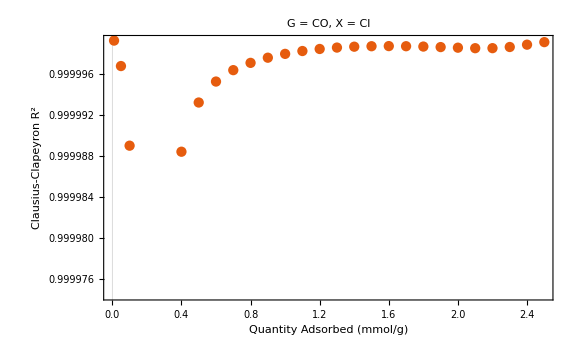

```mathematica
ListPlot[Transpose@{plist,r},PlotTheme->"Scientific",FrameLabel->{"Quantity Adsorbed (mmol/g)","Clausius-Clapeyron R^2"},PlotLabel->"G = CO, X = Cl",ImageSize->Large,FrameStyle->Black]
```

#### Convert results into units of kJ/mol

```mathematica
uddslh=l*-8.31446261815324/1000;
erruddslh=e*-8.31446261815324/1000;
```

#### Plot all of the Clausius-Clapeyron fits, this requires the ErrorBarPlots module. Newer versions of Mathematica will have ErrorBarPlots deprecated and should use ListPlot instead.

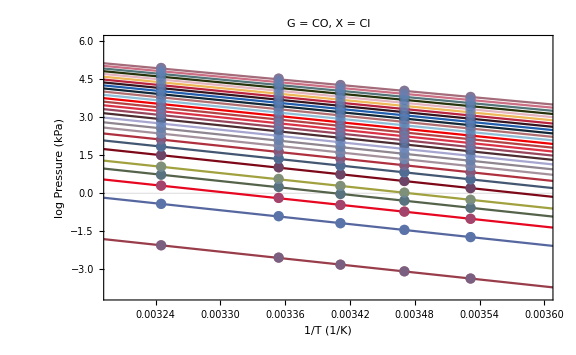

```mathematica
Needs["ErrorBarPlots`"]
Show[Table[ListPlot[Transpose@{temps,uddtot[[i]]},PlotRange->{{0.0032,0.0036},{-4,6}},PlotStyle->ColorData[i,"ColorList"],PlotTheme->"Scientific",FrameLabel->{"1/T (1/K)","log Pressure (kPa)"},PlotLabel->"G = CO, X = Cl"],{i,1,Length[plist]}],Table[Plot[Evaluate[Normal[NonlinearModelFit[Transpose@{temps,uddtot[[i]]},a+b*x,{a,b},x,Weights->1/(Transpose[Transpose[errorsforcc][[1]]][[i]])^2]]],{x,0,1},PlotStyle->ColorData[i,"ColorList"]],{i,1,Length[plist]}],Table[ErrorListPlot[Transpose@{temps,uddtot[[i]],Transpose[Transpose[errorsforcc][[1]]][[i]]},PlotStyle->Directive[Opacity[0.5]]],{i,1,Length[plist]}],ImageSize->Large,FrameStyle->Black]
```

#### Plot the isosteric enthalpy as a function of quantity adsorbed. Newer versions of Mathematica will have ErrorBarPlots deprecated and should use ListPlot instead.

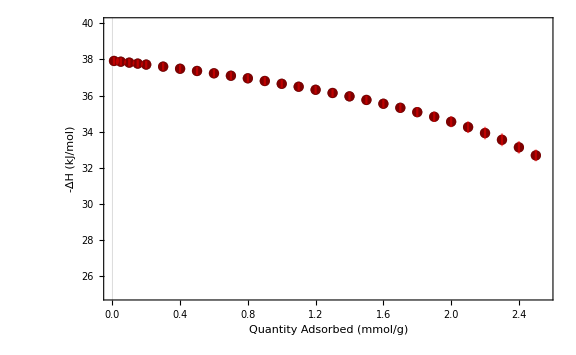

```mathematica
Needs["ErrorBarPlots`"]
Show[ListPlot[Transpose@{plist,uddslh},PlotRange->{{0,2.55},{25,40}},PlotStyle->Black,PlotTheme->"Scientific",FrameLabel->{{"-∆H (kJ/mol)",""},{"Quantity Adsorbed (mmol/g)","G = CO, X = Cl"}},Frame->True,LabelStyle->Directive[Black,FontSize->14]],ErrorListPlot[Transpose@{plist,uddslh,Abs[erruddslh]},PlotStyle->Directive[Opacity[0.5],Red]],ImageSize->Large,FrameStyle->Black]
```

#### Store results into uniquely named variables. This is useful if working across multiple notebook pages.

```mathematica
coclplist=plist
cocl=uddslh
errcocl=erruddslh
```

{0.01,0.05,0.1,0.15,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5}

{37.9119,37.871,37.8189,37.7656,37.7111,37.5986,37.481,37.3582,37.2295,37.0945,36.9528,36.8042,36.649,36.4872,36.3184,36.1415,35.9549,35.757,35.5465,35.3221,35.0825,34.8263,34.5516,34.2541,33.9258,33.5544,33.1366,32.6917}

{-0.210527,-0.210654,-0.211012,-0.2116,-0.212421,-0.214747,-0.217869,-0.221463,-0.224942,-0.227489,-0.228288,-0.226934,-0.223761,-0.219804,-0.216436,-0.214994,-0.216542,-0.221755,-0.23093,-0.244066,-0.260979,-0.281288,-0.304141,-0.327422,-0.346397,-0.353405,-0.343418,-0.323251}